# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can reproduce the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

## Bishop’s Example

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, starting in section 1.1.

Bishop’s Training Set

Create a sequence of Ν=10 inputs for a training set, equally spaced in [0..1].

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

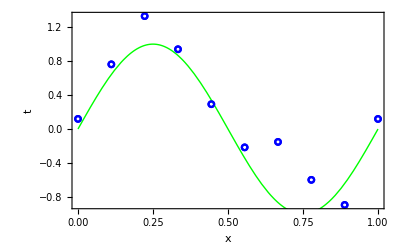

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

Partials: Gradients of the Unknown Parameters

Write a function for partials.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
```

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
Manipulate[Module[{x},
With[{σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
<|"σζ2"->σζ2,"σξ2"-> σξ2,"rrls⟦1⟧"->MatrixForm[goodSolution=rrls⟦1⟧]|>
]]],
Column[{
Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

```mathematica
Dynamic[goodSolution]
```

```mathematica
Manipulate[Module[{x},
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,
ts=bts⟦2⟧,
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{rrlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[rrlsFn,{x,0,1},PlotStyle->{Purple}]];Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]],
Column[{
Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ"},-7,3,Appearance->"Labeled"}]}]]
```

## Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

Initialization

```mathematica
ClearAll[σ0,P,P0,ξ0,ξ0s,importanceFunction];
ClearAll[Ns,σ0,σ,ξ,importanceFunctions,ξs,Μ,Ν,ws];

Ns=200;

Μ=9;
Ν=10;

σ0=10;
σ[0]=List/@ConstantArray[σ0,Μ+1];

ξ[0]=List/@ConstantArray[0.,Μ+1];

importanceFunctions[t_]:=
Table[
NormalDistribution[ξ[t]⟦i,1⟧,σ[t]⟦i,1⟧],
{i,Μ+1}];

ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[importanceFunctions[0]⟦i⟧],
{i,Μ+1},{j,Ns}];

Print[<|"σ"->σ,"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>];

ws[0]=ConstantArray[1./Ns,Ns];
Plus@@ws[0]
```

<|σ→σ,Dimensions[ξs[0]]→{10,200}|>

1.

3D Point Clouds

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

Observations and Residuals

Observations are constant with time, but we include a time parameter for generality. The particle cloud changes with time due to resampling.

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
```

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

Mean and StandardDeviation are documented as column-wise:

```mathematica
ClearAll[residuals,allResiduals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];
(allResiduals=Fold[conjColumns,residuals[0,#]&/@Range[Ns]])//MatrixForm
Mean[allResiduals]//Length
Histogram[Mean[allResiduals]]
```

(-7.32718 | -10.9096 | -2.31209 | -18.9711 | -13.6861 | 9.44974 | -3.55332 | -16.3644 | 8.23251 | -6.19356 | 2.9005 | 4.40622 | 4.32403 | -9.88797 | -10.9978 | 4.96375 | -6.40334 | 12.1171 | -12.3617 | 3.14268 | 14.638 | 2.38653 | 3.45244 | 12.4869 | 11.7069 | 5.76787 | -2.43362 | -12.5652 | 5.8933 | -6.69663 | 3.73854 | -13.6305 | -1.44628 | 4.32631 | 7.10176 | -7.68804 | 12.5868 | 0.0647198 | 5.36316 | 18.4527 | 14.2373 | 14.4361 | 7.39453 | 2.44722 | -3.0573 | -6.1885 | 1.6468 | 7.18973 | 3.09202 | -4.65135 | -2.66086 | -5.3521 | -8.98509 | -6.96061 | 3.41197 | -0.714095 | -3.13024 | 10.8219 | -6.89953 | 13.9697 | 22.11 | -14.0388 | -23.2469 | -21.2129 | 7.90686 | 8.38784 | 13.7197 | -22.5126 | 4.52556 | -3.86008 | 0.434995 | 7.97454 | 6.78197 | -9.00774 | -4.83163 | 10.8251 | 2.61171 | 21.4327 | 9.59262 | -14.6276 | 18.6458 | -5.92479 | 2.23863 | 7.98321 | -6.12829 | 9.51143 | 1.7544 | 26.0081 | 3.06102 | 5.40694 | 0.58968 | 2.16224 | 8.69842 | -2.61172 | -5.54368 | -4.89464 | -0.180794 | -3.01213 | 2.07934 | -9.78301 | 4.27928 | -3.25383 | -0.303111 | -15.9186 | -26.0474 | 1.48503 | -11.1761 | -2.66466 | -12.1228 | 12.0227 | -9.31384 | -3.15818 | -6.84376 | 12.4363 | 0.706761 | 6.22671 | 4.70219 | 17.1545 | 0.815669 | -17.5454 | -13.4599 | 15.2463 | 8.48021 | -7.14812 | -6.90162 | -0.679782 | -3.62986 | 8.51936 | 6.29442 | -5.04383 | -7.94705 | -3.50724 | -7.89884 | 4.28057 | -11.1003 | -7.06114 | 1.77769 | 26.7581 | 9.83217 | -15.9186 | -15.0857 | 11.08 | 21.5667 | -7.87447 | 0.907106 | -1.67756 | 8.63636 | 10.742 | 2.43217 | -10.1176 | -4.53301 | -2.54259 | -10.9866 | 1.22776 | 9.04747 | -0.0803529 | 13.4154 | 2.79928 | -1.24928 | -19.9896 | 6.40561 | 1.00511 | 11.5929 | -21.2256 | -20.1183 | 3.35959 | 9.24264 | -3.73228 | -5.22709 | -1.56269 | 14.9022 | 13.6217 | -2.44094 | -3.9733 | -5.16789 | -2.58607 | -12.96 | -6.65715 | -4.20703 | 8.86916 | 9.27555 | 15.1878 | -12.8139 | -6.79426 | 2.76214 | 6.74978 | 0.515225 | -18.1493 | 5.77587 | -12.3526 | 7.01127 | -1.61869 | 11.27 | -26.0455 | -12.6765 | 3.47766 | -2.56476 | -20.3062 | -9.50104 | -12.9324
-7.62038 | -10.4993 | -3.20509 | -19.9449 | -14.4762 | 8.28136 | -3.1 | -18.0796 | 6.80802 | -7.66555 | 2.54942 | 4.64176 | 5.08374 | -9.74818 | -12.0976 | 2.20082 | -7.1317 | 10.3717 | -13.4954 | 1.35169 | 14.3603 | 0.665387 | 5.05692 | 12.066 | 11.0873 | 4.0484 | -3.16564 | -12.7078 | 4.24479 | -6.44306 | 5.82109 | -14.0406 | -0.160654 | 4.05152 | 5.90729 | -9.4253 | 10.8419 | 1.36585 | 6.2666 | 17.6515 | 16.1517 | 14.8134 | 7.22121 | 2.15066 | -3.53426 | -6.09947 | 0.845016 | 5.48587 | 2.60978 | -7.01437 | -3.23207 | -2.90021 | -9.70316 | -7.03913 | 2.88828 | -1.82053 | -3.00347 | 10.9995 | -10.1908 | 13.5688 | 21.6951 | -14.4607 | -24.5767 | -22.8787 | 6.36965 | 6.10908 | 12.7175 | -22.8273 | 4.5272 | -4.08199 | 0.950434 | 5.65125 | 6.29462 | -9.2131 | -5.87304 | 10.964 | 2.40045 | 21.7778 | 8.37649 | -15.9351 | 18.9909 | -6.09697 | -0.188971 | 6.18164 | -5.68717 | 7.72774 | 1.90779 | 25.269 | 4.11654 | 4.35984 | -1.46268 | 2.44762 | 7.07023 | -2.96514 | -4.3552 | -6.0539 | 0.652536 | -3.24887 | 2.77949 | -10.3914 | 5.02753 | -3.11925 | -0.4506 | -16.524 | -24.7223 | 0.451003 | -11.8515 | -4.15683 | -13.9421 | 12.1669 | -10.7301 | -3.73768 | -8.47079 | 12.8173 | 0.101915 | 4.54717 | 4.66944 | 15.4775 | -0.467342 | -16.4678 | -13.1133 | 15.7704 | 6.79248 | -7.65421 | -9.1916 | -0.377182 | -4.32344 | 5.8397 | 4.9322 | -6.85141 | -8.58455 | -3.91721 | -7.79933 | 5.9651 | -10.8182 | -7.4577 | -0.414574 | 25.8643 | 10.9953 | -16.0677 | -14.8631 | 11.1441 | 20.6197 | -9.05389 | -1.35447 | -2.78851 | 8.0376 | 9.65149 | 1.39369 | -8.69129 | -3.82939 | -2.41701 | -11.8751 | 0.239213 | 8.59257 | -0.650958 | 11.6938 | 2.65133 | -1.64737 | -20.7151 | 6.00512 | 1.63773 | 10.6637 | -22.6357 | -20.9843 | 3.60846 | 10.0174 | -3.1005 | -3.82725 | -5.00542 | 14.9085 | 13.9031 | -4.59309 | -6.02114 | -7.51815 | -1.67244 | -13.9379 | -6.86656 | -3.93405 | 7.88619 | 9.53467 | 13.9339 | -12.0398 | -8.59202 | 2.14282 | 7.65534 | 0.924452 | -18.9415 | 5.56123 | -13.8642 | 8.67765 | -2.39751 | 10.6043 | -26.716 | -13.0521 | 2.49387 | -6.59364 | -21.8181 | -9.9597 | -13.777
-7.48238 | -10.2268 | -3.64888 | -20.5597 | -15.082 | 7.06916 | -2.10659 | -19.4933 | 5.59877 | -8.92738 | 2.49307 | 5.02151 | 5.86928 | -9.09675 | -13.0481 | -0.238593 | -7.73061 | 8.55623 | -14.7079 | -0.524673 | 14.7567 | -0.81687 | 6.51007 | 11.841 | 10.5215 | 2.25917 | -3.90048 | -12.6526 | 2.94927 | -6.06161 | 8.33989 | -14.5756 | 1.09214 | 3.88189 | 4.22395 | -11.1078 | 9.38605 | 2.83672 | 7.40146 | 16.6233 | 17.5955 | 15.3522 | 7.61263 | 1.77567 | -3.69582 | -5.76241 | 0.180124 | 3.74853 | 2.25424 | -9.4401 | -3.64867 | 0.0689959 | -10.2617 | -6.91015 | 2.52774 | -2.52216 | -2.82956 | 11.4581 | -13.2201 | 12.637 | 21.0397 | -14.7393 | -25.9268 | -24.8117 | 4.91786 | 3.6798 | 12.1057 | -22.8235 | 4.90814 | -4.29551 | 1.48052 | 3.06413 | 5.8579 | -9.66203 | -6.81926 | 11.1905 | 2.19012 | 22.7397 | 6.9918 | -16.7565 | 19.9114 | -6.18278 | -2.50739 | 4.33847 | -5.05627 | 6.05456 | 2.32684 | 24.5398 | 5.34042 | 3.3542 | -3.3088 | 2.68842 | 5.47816 | -3.33136 | -3.33299 | -6.78269 | 1.50575 | -3.22731 | 3.71001 | -10.9266 | 6.01783 | -2.79825 | -0.353007 | -17.0453 | -23.1133 | -0.99563 | -13.1738 | -5.35429 | -15.535 | 12.7959 | -11.9722 | -4.105 | -9.90767 | 13.1747 | -0.859202 | 3.11542 | 5.30686 | 13.5875 | -1.7881 | -15.3293 | -12.1167 | 16.4703 | 5.41405 | -8.19542 | -11.9676 | 0.265965 | -5.03971 | 3.25718 | 3.38835 | -8.65492 | -9.67497 | -4.28349 | -7.4542 | 8.03892 | -10.2818 | -8.08039 | -2.56072 | 24.5967 | 12.2481 | -16.3007 | -14.5553 | 11.03 | 19.3586 | -10.8536 | -3.83942 | -3.83173 | 7.49368 | 8.44769 | 0.848629 | -7.44233 | -2.54771 | -1.53068 | -12.736 | -1.00933 | 8.12088 | -1.16311 | 10.3515 | 3.20944 | -1.92494 | -21.2223 | 5.6147 | 1.98239 | 9.66963 | -24.1313 | -21.2444 | 3.84447 | 10.9576 | -2.32521 | -2.23225 | -8.13003 | 14.7351 | 14.7553 | -6.96758 | -7.88781 | -9.79356 | -0.746088 | -15.0596 | -6.83677 | -3.70858 | 6.6148 | 9.67112 | 13.0353 | -10.9855 | -10.3926 | 1.55513 | 8.37378 | 1.25789 | -19.3529 | 5.66315 | -15.8651 | 9.85542 | -3.11288 | 10.0245 | -27.6196 | -13.2503 | 1.72028 | -10.2333 | -23.1856 | -10.5726 | -14.64
-5.94555 | -9.26439 | -2.72591 | -19.751 | -14.6548 | 6.38817 | 0.306702 | -19.5502 | 5.63626 | -9.04528 | 3.65138 | 6.47436 | 7.44304 | -7.14923 | -12.9767 | -1.57084 | -7.24671 | 7.47826 | -15.0482 | -1.53808 | 16.8086 | -1.02938 | 8.66484 | 12.6664 | 10.6864 | 1.28462 | -3.80616 | -11.6256 | 3.03454 | -4.74403 | 12.2292 | -14.5197 | 3.17219 | 4.868 | 2.8259 | -11.8414 | 9.26131 | 5.39866 | 9.67235 | 16.2317 | 19.5292 | 16.9877 | 9.57828 | 2.27602 | -2.65412 | -4.31909 | 0.503237 | 2.9806 | 2.8715 | -11.0281 | -3.08795 | 4.51767 | -9.79932 | -5.66419 | 3.317 | -1.92519 | -1.66696 | 13.0174 | -14.9166 | 11.9628 | 21.0558 | -14.1422 | -26.4654 | -26.2951 | 4.40605 | 1.92326 | 12.7061 | -21.5843 | 6.60953 | -3.46281 | 2.8802 | 1.03154 | 6.41644 | -9.43747 | -6.82486 | 12.4804 | 2.71853 | 25.2564 | 6.18192 | -16.1022 | 22.3532 | -5.4167 | -3.73713 | 3.23709 | -3.39437 | 5.33272 | 3.94298 | 24.6889 | 7.59318 | 3.25513 | -4.00693 | 3.6323 | 4.87763 | -2.75166 | -1.59605 | -6.08305 | 3.16535 | -2.09792 | 5.83227 | -10.5196 | 8.2289 | -1.33896 | 0.859123 | -16.5714 | -20.3062 | -2.04855 | -14.49 | -5.53401 | -16.0498 | 14.6869 | -12.0644 | -3.40436 | -10.1924 | 14.3118 | -1.34367 | 2.73249 | 7.41314 | 12.3405 | -2.17964 | -13.3448 | -9.50811 | 18.1994 | 5.20915 | -7.86286 | -14.4397 | 2.23595 | -4.93841 | 1.73451 | 2.41606 | -9.64923 | -10.6095 | -3.80273 | -6.05134 | 11.55 | -8.43993 | -7.96126 | -3.76014 | 23.5802 | 14.387 | -15.8866 | -13.287 | 11.565 | 18.6549 | -12.3513 | -5.71005 | -3.83177 | 7.97491 | 7.99363 | 1.68482 | -5.47945 | 0.285779 | 1.11378 | -12.5683 | -1.65137 | 8.57679 | -0.744895 | 10.3234 | 5.4521 | -1.18948 | -20.6161 | 6.18625 | 2.84476 | 9.48831 | -24.7104 | -20.0288 | 4.85784 | 13.057 | -0.474639 | 0.529152 | -9.87153 | 15.2106 | 17.1026 | -8.69704 | -8.71367 | -10.954 | 0.942475 | -15.3439 | -5.51272 | -2.66655 | 5.98325 | 10.4588 | 13.3573 | -8.76452 | -11.2785 | 1.96957 | 9.87778 | 2.39718 | -18.4414 | 7.02332 | -17.5037 | 11.3321 | -2.73025 | 10.1547 | -27.8388 | -12.386 | 2.02232 | -12.4245 | -23.4996 | -10.6816 | -14.6695
-3.55462 | -8.53871 | -1.19749 | -18.032 | -13.965 | 5.23904 | 3.38354 | -18.8303 | 6.40388 | -8.54219 | 5.3259 | 8.35393 | 8.99924 | -4.69942 | -12.642 | -2.56205 | -6.27064 | 6.38027 | -15.1385 | -2.34877 | 19.9711 | -0.48817 | 10.8301 | 13.718 | 10.6996 | 0.385549 | -3.65907 | -10.446 | 4.01084 | -3.23793 | 16.7986 | -14.7885 | 5.39422 | 6.58239 | 0.832272 | -12.3354 | 9.93786 | 8.36648 | 12.3877 | 15.7535 | 21.4033 | 19.022 | 12.528 | 3.1127 | -1.09177 | -2.56177 | 0.983634 | 2.59215 | 3.65707 | -12.4472 | -2.30216 | 9.87421 | -9.05543 | -3.95835 | 4.58685 | -0.732433 | -0.141568 | 14.8197 | -15.6961 | 10.7682 | 21.0766 | -13.6418 | -27.031 | -28.2327 | 4.12229 | 0.115138 | 13.7351 | -19.7313 | 9.02975 | -2.10581 | 4.42736 | -1.17992 | 7.31076 | -9.18609 | -6.66731 | 14.1977 | 3.13211 | 28.6809 | 4.98838 | -14.5371 | 25.6307 | -4.79859 | -4.47242 | 2.05277 | -1.46505 | 4.73738 | 6.17347 | 25.0573 | 10.1775 | 3.29713 | -4.18993 | 4.39063 | 4.63707 | -1.85439 | 0.217626 | -4.56283 | 4.73475 | -0.552971 | 8.57837 | -9.90973 | 11.1883 | 0.722967 | 2.39615 | -15.7769 | -16.9941 | -3.49827 | -16.7256 | -5.64735 | -16.2638 | 16.8951 | -11.6354 | -2.34312 | -9.91667 | 15.4339 | -2.0388 | 2.51677 | 10.1665 | 11.1011 | -2.21409 | -11.3693 | -5.83225 | 20.2342 | 5.53896 | -7.40915 | -17.4727 | 5.00434 | -4.86166 | 0.637599 | 1.18099 | -10.5856 | -12.4976 | -3.20737 | -4.29662 | 15.9813 | -5.79987 | -7.62698 | -4.57512 | 21.7947 | 16.5784 | -15.6519 | -11.7675 | 12.0099 | 17.7955 | -14.163 | -7.75097 | -3.37958 | 8.93913 | 7.6013 | 3.16443 | -3.44829 | 4.09929 | 5.06394 | -11.8276 | -2.42942 | 9.26693 | -0.0802863 | 11.0069 | 8.83162 | -0.150879 | -19.497 | 7.14903 | 3.45822 | 9.38732 | -24.9152 | -18.1589 | 5.80438 | 15.8381 | 1.89953 | 3.9165 | -10.6708 | 15.5841 | 20.2404 | -10.4851 | -9.26239 | -11.5073 | 2.54756 | -15.3165 | -3.47081 | -1.53303 | 5.36661 | 11.0635 | 14.1988 | -6.06452 | -11.8377 | 2.86273 | 11.5896 | 3.6354 | -16.8661 | 9.02396 | -19.678 | 12.3667 | -1.72722 | 9.93054 | -28.0154 | -11.2419 | 2.66055 | -13.6121 | -23.4464 | -11.2709 | -14.4723
-0.505783 | -9.05179 | 0.310222 | -15.6113 | -13.5259 | 2.95927 | 6.58067 | -17.7173 | 7.69877 | -7.43875 | 7.11932 | 10.3597 | 9.96395 | -2.17717 | -12.5194 | -3.6387 | -5.00659 | 4.85454 | -15.2485 | -3.42673 | 24.1164 | 0.60717 | 12.6884 | 14.2639 | 10.0994 | -0.93356 | -4.02574 | -9.64336 | 5.7964 | -1.91847 | 21.5913 | -16.0745 | 7.52743 | 9.08003 | -2.41603 | -13.009 | 11.2064 | 11.2783 | 15.2134 | 14.8238 | 23.1121 | 20.8511 | 16.1284 | 4.20145 | 0.756063 | -1.07743 | 0.960241 | 2.29639 | 3.97683 | -14.0063 | -1.71769 | 15.9405 | -8.52037 | -2.14352 | 5.80941 | 0.628552 | 1.46219 | 16.0991 | -15.5121 | 8.563 | 20.8076 | -14.1568 | -28.2773 | -31.2062 | 3.69748 | -2.07731 | 14.6961 | -17.5037 | 11.9657 | -0.408394 | 5.65968 | -3.95827 | 8.15681 | -9.25008 | -6.88507 | 15.9712 | 2.93991 | 32.7572 | 2.68189 | -12.294 | 29.2339 | -5.38172 | -5.08552 | 0.155556 | 0.306595 | 3.57564 | 8.78847 | 25.3187 | 12.7311 | 2.93282 | -4.08309 | 4.27817 | 4.4898 | -0.9437 | 1.89573 | -2.5838 | 5.42872 | 1.17507 | 11.8308 | -9.63144 | 14.9886 | 3.37911 | 3.6182 | -15.0582 | -13.672 | -5.94375 | -20.4644 | -6.46102 | -16.7815 | 18.4942 | -11.1116 | -1.32135 | -9.38068 | 16.0433 | -3.21624 | 1.79745 | 13.0116 | 9.66845 | -2.14951 | -10.0168 | -1.20917 | 22.1931 | 6.19073 | -7.3806 | -21.6813 | 8.39676 | -5.487 | -0.362363 | -0.890992 | -11.7965 | -16.2357 | -2.78205 | -2.4753 | 21.1746 | -2.53091 | -7.1801 | -4.95273 | 18.4699 | 18.1309 | -16.0188 | -10.4115 | 11.9713 | 16.3989 | -16.5322 | -10.4443 | -2.68806 | 10.2824 | 7.00507 | 4.73792 | -1.54188 | 8.63406 | 10.4187 | -10.4653 | -3.76969 | 9.75407 | 0.529218 | 12.2714 | 13.2354 | 0.745161 | -17.9959 | 8.34593 | 3.39662 | 8.89569 | -24.9084 | -16.2783 | 5.99807 | 19.2551 | 4.73258 | 7.84562 | -10.5183 | 15.4387 | 23.7148 | -12.5032 | -10.1266 | -11.582 | 3.53857 | -14.9878 | -1.14435 | -0.699464 | 4.48718 | 10.9194 | 15.2284 | -3.19852 | -12.2719 | 4.07594 | 13.3053 | 4.47977 | -15.0354 | 11.3668 | -23.2746 | 12.7079 | -0.204402 | 8.47717 | -28.4379 | -10.4289 | 3.20371 | -13.7579 | -23.4923 | -13.0772 | -14.1689
2.9343 | -12.6666 | 0.813452 | -12.7497 | -13.9492 | -1.05793 | 9.10668 | -16.8385 | 9.27653 | -5.48634 | 8.6535 | 12.2698 | 9.43482 | 0.150264 | -13.0741 | -5.239 | -3.50316 | 2.57836 | -15.559 | -5.61585 | 29.2497 | 1.94852 | 13.9614 | 13.1227 | 8.63881 | -3.34892 | -5.74491 | -9.83729 | 8.37952 | -1.10545 | 26.0468 | -19.2907 | 9.68803 | 12.6478 | -7.66906 | -14.3232 | 12.8453 | 13.3754 | 17.9738 | 13.1568 | 24.7415 | 21.2115 | 19.8653 | 5.57248 | 3.0806 | -0.654613 | -0.382314 | 1.838 | 2.86559 | -15.8821 | -1.7186 | 22.5946 | -8.84267 | -0.628172 | 6.06242 | 1.65745 | 2.84714 | 15.6172 | -14.1064 | 4.70628 | 20.1858 | -17.1881 | -30.9936 | -35.6116 | 2.82029 | -4.8479 | 15.0471 | -15.0603 | 15.3488 | 1.46347 | 5.89089 | -7.66046 | 8.50421 | -10.0106 | -8.18321 | 17.3485 | 1.77921 | 37.4691 | -1.44389 | -9.60252 | 32.3414 | -8.91531 | -6.30826 | -3.5515 | 1.62757 | 0.827864 | 11.5122 | 25.0687 | 14.9016 | 1.42363 | -3.63637 | 2.37863 | 4.37447 | -0.271318 | 3.39613 | -0.688174 | 4.07149 | 3.22312 | 15.7151 | -10.525 | 20.1859 | 7.04784 | 3.53718 | -14.9587 | -11.1316 | -10.3492 | -26.1681 | -8.95611 | -18.5542 | 17.9418 | -11.1991 | -0.874612 | -9.0273 | 15.5902 | -5.00552 | -0.158711 | 15.3419 | 7.94929 | -2.38231 | -10.0166 | 4.37484 | 23.7312 | 7.09997 | -8.44467 | -27.786 | 12.2276 | -7.748 | -1.61288 | -4.61024 | -13.3098 | -22.6677 | -2.55767 | -0.653486 | 27.0755 | 1.18912 | -6.63167 | -4.22199 | 12.8035 | 17.9122 | -17.3356 | -9.7213 | 11.0889 | 14.1636 | -19.5829 | -14.2217 | -1.86046 | 12.0883 | 6.20679 | 5.54428 | 0.36869 | 13.4959 | 17.721 | -8.15605 | -5.99367 | 9.53194 | 0.908442 | 14.3027 | 18.7878 | 0.936662 | -15.9768 | 9.82409 | 2.25414 | 7.36129 | -24.7461 | -15.1615 | 4.40804 | 23.2822 | 8.22579 | 12.4918 | -9.14245 | 14.3922 | 26.9792 | -14.2561 | -12.2409 | -11.2095 | 3.39652 | -13.8962 | 0.606249 | -0.434442 | 3.07607 | 9.32031 | 16.2677 | -0.374261 | -12.8204 | 5.44707 | 14.9183 | 4.07707 | -13.5174 | 13.6688 | -29.7437 | 12.4941 | 1.74148 | 4.77992 | -29.3214 | -10.834 | 3.23807 | -12.5937 | -24.4014 | -16.8903 | -13.7121
7.81298 | -21.4168 | 0.239789 | -8.21729 | -14.4108 | -5.65665 | 11.1614 | -15.6815 | 12.4811 | -0.449091 | 11.2334 | 15.6732 | 7.29437 | 4.05381 | -13.0261 | -6.24675 | 0.136663 | 1.06904 | -14.4387 | -9.04485 | 37.0837 | 4.47422 | 15.9001 | 9.90282 | 8.00894 | -6.37806 | -8.60829 | -10.2852 | 13.2712 | 0.451444 | 31.2035 | -24.2481 | 14.3465 | 19.4571 | -14.0697 | -15.1975 | 16.199 | 14.7219 | 22.4877 | 12.1177 | 28.226 | 18.8701 | 24.3718 | 8.78361 | 8.73808 | -0.830936 | -2.24795 | 2.73996 | 0.24837 | -16.2982 | -0.915766 | 31.4438 | -9.39928 | 1.65771 | 5.19053 | 3.39746 | 5.15013 | 12.8768 | -9.31876 | -0.25064 | 21.4329 | -23.8658 | -34.3983 | -39.5693 | 2.90562 | -6.52035 | 15.7851 | -10.8582 | 20.923 | 4.98006 | 5.4571 | -10.9755 | 9.39657 | -10.2779 | -10.0017 | 19.3606 | 1.12746 | 44.9738 | -6.20122 | -5.06667 | 35.1573 | -16.7836 | -8.19883 | -9.81303 | 4.17461 | -3.39245 | 15.4965 | 25.2666 | 17.9435 | -0.681089 | -0.551224 | -1.05185 | 6.3939 | 1.68737 | 6.544 | 1.77914 | 0.397765 | 8.15613 | 22.3608 | -12.5064 | 29.7959 | 14.5823 | 2.11253 | -14.8224 | -9.15655 | -16.8671 | -32.3174 | -12.8896 | -21.6684 | 14.1246 | -11.5305 | -0.421055 | -8.02047 | 15.0029 | -5.69535 | -2.42708 | 18.1712 | 7.49376 | -2.07836 | -10.6671 | 12.7032 | 26.1224 | 10.0408 | -9.73665 | -35.1789 | 17.8464 | -11.4186 | -1.93288 | -9.88418 | -12.7998 | -30.5687 | -0.572878 | 3.19827 | 35.4677 | 6.6957 | -4.39181 | 1.04933 | 5.67889 | 15.4718 | -18.484 | -8.83915 | 10.641 | 12.6594 | -21.5061 | -17.7178 | 0.731596 | 16.3256 | 7.38798 | 5.68393 | 4.69934 | 19.4613 | 30.002 | -2.5334 | -7.43993 | 9.61623 | 2.71764 | 19.4108 | 27.6776 | 1.23 | -11.2344 | 13.6961 | 1.18347 | 5.23106 | -22.688 | -14.0181 | 0.99515 | 29.2465 | 14.5557 | 20.0826 | -4.11767 | 13.7031 | 30.9928 | -12.0924 | -15.593 | -8.68514 | 3.21416 | -8.94765 | 1.65603 | 1.01762 | 2.403 | 6.78432 | 19.1179 | 3.9394 | -12.4691 | 8.39519 | 18.0833 | 2.26626 | -11.6153 | 16.8344 | -39.9729 | 14.2273 | 5.49315 | -0.736617 | -29.0925 | -12.2517 | 4.03345 | -8.02964 | -26.0244 | -21.8582 | -11.3928
12.8852 | -42.3436 | -4.35216 | -2.5427 | -15.9625 | -10.8591 | 9.96501 | -16.1683 | 17.2644 | 8.85447 | 14.7655 | 21.0752 | 0.143047 | 10.7117 | -12.2175 | -7.17444 | 6.91951 | 0.852643 | -11.3804 | -17.2686 | 47.6655 | 6.6844 | 17.7955 | 1.26062 | 8.73922 | -12.1078 | -14.9981 | -12.3765 | 19.9023 | 2.11527 | 36.9107 | -33.3874 | 23.857 | 30.3681 | -22.0459 | -16.2197 | 20.9613 | 12.0262 | 29.7995 | 11.3315 | 34.1689 | 7.74478 | 27.6886 | 13.2341 | 21.2745 | -3.29643 | -4.85053 | 5.42821 | -6.96279 | -14.2505 | 0.996323 | 42.7423 | -11.8186 | 3.99169 | -0.20224 | 5.39103 | 7.35677 | 4.39523 | -0.162081 | -8.24776 | 26.8225 | -39.3417 | -39.0144 | -41.0551 | 4.01433 | -6.47958 | 16.2596 | -4.8 | 29.1759 | 10.1303 | 1.84737 | -13.9974 | 10.0965 | -10.3951 | -13.9972 | 21.2731 | 1.2495 | 57.0212 | -11.1544 | 1.24691 | 35.3411 | -34.0587 | -14.4213 | -23.6934 | 8.84255 | -11.094 | 19.9767 | 24.8087 | 21.5384 | -4.85781 | 7.21149 | -8.07875 | 12.3259 | 5.3094 | 11.9987 | 3.04871 | -8.60561 | 18.6109 | 32.9614 | -18.3966 | 46.7942 | 28.8108 | -3.40361 | -16.5027 | -10.1761 | -28.7013 | -38.0564 | -20.2968 | -29.2453 | 2.26913 | -14.1853 | -2.23267 | -7.67136 | 13.374 | -4.6836 | -5.39925 | 21.1945 | 8.17261 | -2.67608 | -13.089 | 24.2098 | 28.9647 | 15.6493 | -11.883 | -45.5466 | 24.9089 | -18.6119 | -1.98726 | -19.9067 | -7.9366 | -38.9671 | 4.01618 | 10.5666 | 47.0274 | 13.4763 | -0.701392 | 14.7293 | -3.26896 | 7.07312 | -20.6761 | -9.06571 | 10.3737 | 12.5651 | -21.2336 | -20.676 | 5.18461 | 23.7932 | 12.2464 | 2.48661 | 13.6183 | 24.7117 | 50.4709 | 7.92861 | -7.06002 | 9.34077 | 6.44993 | 29.0539 | 41.37 | 0.399876 | -2.35201 | 21.4721 | -0.487059 | 0.18887 | -18.2236 | -13.4287 | -6.79475 | 36.0943 | 24.758 | 31.9825 | 6.54126 | 13.0354 | 35.1082 | -0.799157 | -22.8644 | -3.73651 | 2.43826 | 3.43459 | -1.26891 | 4.90738 | 1.91913 | 1.37359 | 24.8103 | 9.81222 | -12.8279 | 12.8175 | 23.1014 | -4.64698 | -10.8714 | 19.3721 | -58.3174 | 20.1792 | 10.4978 | -9.48951 | -27.3113 | -16.9581 | 5.49278 | 0.503879 | -31.1722 | -28.4284 | -7.33606
15.229 | -88.9325 | -18.4053 | 3.31344 | -20.3936 | -16.0027 | -0.38088 | -21.9594 | 24.1055 | 24.0781 | 19.2959 | 29.8424 | -18.8024 | 23.0869 | -9.58773 | -8.68726 | 18.9209 | 3.53899 | -5.17346 | -37.537 | 60.2318 | 5.09165 | 17.7131 | -18.5468 | 11.537 | -24.8202 | -29.2098 | -18.8349 | 26.0975 | 2.13224 | 44.1714 | -51.3824 | 42.9992 | 46.1559 | -31.2917 | -18.3133 | 26.5077 | -1.82561 | 42.241 | 9.50446 | 43.1026 | -24.6186 | 25.6127 | 16.5182 | 48.3965 | -10.8049 | -6.71788 | 11.1646 | -24.7519 | -7.27762 | 5.29712 | 56.9411 | -19.25 | 5.1253 | -16.805 | 7.44351 | 6.83358 | -15.6168 | 14.673 | -23.217 | 41.8225 | -73.5019 | -44.657 | -34.543 | 6.36346 | -3.33388 | 15.5908 | 3.22521 | 40.894 | 16.9623 | -10.1431 | -16.5928 | 9.2673 | -10.661 | -23.1516 | 21.8288 | 2.71976 | 77.3521 | -14.2844 | 9.4203 | 28.8514 | -69.4692 | -32.8058 | -55.745 | 17.8383 | -24.9179 | 23.4879 | 21.5697 | 25.1919 | -13.3256 | 23.9537 | -22.1675 | 26.2305 | 11.6869 | 20.8664 | -0.506063 | -28.0501 | 40.0541 | 49.5309 | -33.5851 | 76.6118 | 55.135 | -17.7625 | -23.9491 | -18.5923 | -51.741 | -40.8152 | -34.7021 | -47.2954 | -26.0715 | -22.7445 | -11.606 | -10.3575 | 9.1343 | -0.593854 | -9.09555 | 24.7588 | 9.33569 | -6.87036 | -18.9218 | 39.4888 | 31.2674 | 25.2378 | -15.2984 | -62.4224 | 32.7547 | -32.9039 | -3.38809 | -41.7121 | 6.39504 | -44.1916 | 12.1834 | 24.7392 | 63.081 | 20.2013 | 3.21862 | 43.7879 | -13.8253 | -14.1344 | -27.3996 | -13.1389 | 9.92126 | 15.8424 | -16.0257 | -22.0932 | 11.1429 | 35.6533 | 24.1673 | -8.97769 | 31.5045 | 25.1647 | 85.4807 | 25.833 | -1.93294 | 7.69733 | 13.0985 | 45.3477 | 62.6304 | -3.81729 | 13.1715 | 36.3428 | -4.31792 | -12.7371 | -10.435 | -13.4752 | -22.977 | 40.8039 | 40.0369 | 50.4082 | 26.8409 | 11.6479 | 38.6793 | 30.4304 | -38.6787 | 3.79995 | -0.00513965 | 30.4678 | -14.267 | 14.5966 | 0.284191 | -10.8498 | 35.7479 | 17.113 | -18.0859 | 18.7357 | 30.3389 | -24.3295 | -14.235 | 17.8138 | -92.6582 | 34.6491 | 15.268 | -23.6471 | -22.7848 | -28.9532 | 7.77257 | 13.0322 | -45.378 | -36.4709 | -2.77372)

New Weights

What is the probability of each particle ξ given its corresponding Ν observations ζ?

```mathematica
PDF[NormalDistribution[μ,σ]]
```

Function[x,(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)]

Assuming that the residuals have zero theoretical mean, the chances of observing a particular residual are roughly:

{0.00373136,9.78096×10^-9,0.00520057,0.0184074,«192»,0.00654623,9.21526×10^-20,0.00628936,0.00588441}

1.

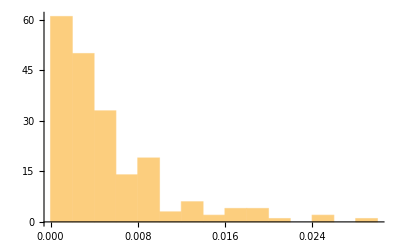

```mathematica
ClearAll[pres];
pres[samp_]:=
With[{var=scalar@Variance[samp],x=scalar@Mean[samp],μ=0},
1/(√(2.π var))Exp[-(x-μ)^2/(2var)]];
ws[1]=
With[{ps=pres[residuals[0,#]]&/@Range[Ns]},
With[{s=Plus@@ps},
ps/s]];
ws[1]//Short[#,3]&
Plus@@ws[1]
Histogram[ws[1]]
```

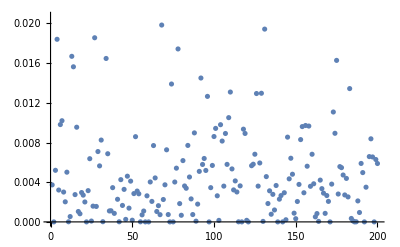

```mathematica
ListPlot[ws[1]]
```

Cull Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights];
(indexedWeights=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,0.00373136},«198»,{200,0.00588441}}

Keep the top p%. In general, p should be the reciprocal of an integer that divides N_s because we are going to copy each survivor 1/p times to make a new sample of size N_s.

```mathematica
ClearAll[p,sortedIndexedWeights,topPWeights,topPIndexedWeights,topPIndices,topPParticles];
p=0.10;
<|"sortedIndexedWeights"->((sortedIndexedWeights=Reverse@SortBy[indexedWeights,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights=sortedIndexedWeights⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights=Last/@topPIndexedWeights)//Short),
"topPIndices"->((topPIndices=First/@topPIndexedWeights)//Short),
"topPParticles//Dims"->((topPParticles=(ξs[0]⟦All,#⟧&/@topPIndices)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{33,0.0291922},«198»,{198,9.21526×10^-20}},topPIndexedWeights→{{33,0.0291922},«18»,{96,0.0126521}},topPWeights→{0.0291922,0.0256956,«17»,0.0126521},topPIndices→{33,122,40,194,68,131,27,4,78,13,34,175,14,92,74,183,110,129,126,96},topPParticles//Dims→{10,20},top 3 Particles→(0.58038 | -3.14512 | -1.63181
-14.0779 | 4.28323 | 6.43506
23.4628 | -9.35698 | -9.65129
-13.0726 | 12.9491 | 7.37414
-1.02078 | 9.27477 | -0.284951
5.49855 | 2.50184 | 5.76652
-0.704648 | -5.99425 | -0.143672
-0.803934 | -8.73991 | 6.187
5.54256 | 8.01489 | -9.86421
-0.362412 | -8.28845 | 1.4793)|>

Structure emerges after culling.

```mathematica
threeDPointClouds[topPParticles,σ0]
```

Top p Particles

Replace each particle with 1/p copies, each perturbed by this new σ_1. There are other ways to compute an importance sample of the top p particles. One way, possibly biased, is to keep the original survivor and add 1/p-1 perturbed copies. We first perform this latter sample (original joined to three copies) to check matrix dimensions, but proceed with the former sample (four copies).

### Standard Deviations

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles
```

{3.61035,8.34638,10.0565,8.54893,9.88918,8.55617,8.2386,8.75036,7.23184,11.511}

### Unbiased? Importance Sample

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]},
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]];
make1OverP[topPParticles⟦All,4⟧,σξ[1],p]//MatrixForm
```

(7.26272 | -1.83848 | -0.0672637 | 2.6877 | -3.07876 | 0.0663341 | 3.23348 | 3.5036 | 3.0044 | 1.44279
8.24448 | -13.0955 | -14.961 | -23.285 | -23.086 | -12.5163 | -19.9819 | -1.68521 | -13.8627 | -8.87409
3.05467 | 7.11323 | 4.02794 | -9.85032 | -10.1279 | -5.35361 | 11.4585 | -24.5678 | -26.8436 | -3.24798
3.03424 | 16.8491 | 15.7698 | -1.0091 | 6.81635 | 23.293 | 12.3511 | 10.6839 | 9.08264 | -3.6545
9.99736 | 11.2869 | 5.44952 | -14.4089 | 2.71983 | 20.7725 | 19.8463 | 5.73276 | -0.260641 | 21.0128
12.4799 | 22.1567 | 17.0673 | 9.87754 | 16.1063 | 2.92651 | 4.25521 | -2.83272 | 15.1174 | 13.3545
-3.20787 | -8.1288 | 9.27048 | 9.0313 | -18.7056 | -11.1883 | -2.73581 | 5.72416 | -3.56546 | -23.9128
5.99939 | -1.46958 | 10.6775 | 4.55229 | 0.945521 | -3.12407 | -1.88001 | -6.80256 | -6.29207 | 5.26793
-19.9256 | 0.331359 | -12.8335 | -0.513758 | 2.34481 | 8.04673 | -13.4421 | 0.87466 | -16.46 | 2.36321
-7.80665 | 8.8988 | 11.6906 | 15.9208 | 8.91704 | 18.4247 | 2.52006 | -14.5446 | -1.93994 | 20.0672)

New Particle Cloud

```mathematica
topPParticles//Dimensions
```

{10,20}

```mathematica
(ξs[1]=Fold[conjColumns,make1OverP[#,σξ[1],p]&/@(topPParticlesᵀ)])//Dimensions
```

{10,200}

```mathematica
threeDPointClouds[ξs[1],σ0]
```

```mathematica
StandardDeviation/@ξs[0]
```

{9.50983,10.7601,9.64612,9.97181,10.3311,10.1604,10.2184,10.6844,10.3126,10.4145}

```mathematica
StandardDeviation/@ξs[1]
```

{5.26441,11.6522,13.8723,11.6113,13.4855,12.0525,12.0222,12.7777,9.68273,14.8867}

one goes down, the others go up.

Package and Experiment

Abstract the procedures above and iterate.

We have some global variables, namely Μ and N_s. Assert that input dimensions match expectations w.r.t. these globals.

Add a regularization parameter, λ, to penalize particles of large norm.

```mathematica
ClearAll[looseThreeDPointClouds];
looseThreeDPointClouds[ξs_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
```

#### Old $ #! &

```mathematica
ClearAll[ssrFn,prFn,regula,weights,cull,iterate];
On[Assert];
ssrFn[A_,ζ_][ξ_]:=(* Alternative cost function to 1/p *)
With[{ress=ζ-A.ξ},
With[{ssr=ressᵀ.ress},
scalar@ssr]];
prFn[A_,ζ_][ξ_]:=pres[ζ-A.ξ];
regula[λ_][ξ_]:=(λ(ξ.ξ));
weights[xs_,ζ_,λ_][ξs_]:=
With[{A=partialsFn[Μ,xs]},
(Assert[Μ+1===Length[xs]];
Assert[Μ+1===Length[ζ]];
Assert[{Μ+1,Ns}===Dimensions[ξs]];
With[{cost=(regula[λ]/@(ξsᵀ))+(1./prFn[A,ζ]/@(ξsᵀ))},
With[{wpre=cost},
With[{ws= 1/cost/Plus@@(1/cost)},
Assert[Ns===Length[ws]];
Assert[Round[Plus@@ws,10.^-6]===1.];
ws]]])];
cull[xs_,ζ_,λ_][p_,ξs_]:=Module[{indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPWeights,topPIndices,topPParticles},
indexedWeights=Function[ws,MapThread[List,{Range[Ns],ws}]];
sortedIndexedWeights=Function[ws,Reverse@SortBy[indexedWeights[ws],Last]];
topPIndexedWeights=Function[ws,sortedIndexedWeights[ws]⟦;;Floor[p Ns]⟧];
topPIndices=Function[ws,First/@topPIndexedWeights[ws]];
topPWeights=Function[ws,Last/@topPIndexedWeights[ws]];
topPParticles=Function[ws,
With[{result=(ξs⟦All,#⟧&/@topPIndices[ws])ᵀ},
Assert[{Μ+1,Floor[p Ns]}===Dimensions[result]];
result]];
topPParticles[weights[xs,ζ,λ][ξs]]];
iterate[xs_,ζ_,λ_][p_,ξs_]:=
With[{culled=cull[xs,ζ,λ][p,ξs]},
With[{σξ=0.5StandardDeviation/@culled},
With[{result=Fold[
conjColumns,
make1OverP[#,σξ,p]&/@(culledᵀ)]},
Assert[{Μ+1,Ns}===Dimensions[result]];
result]]];
```

```mathematica
Manipulate[
With[{top=
cull[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][0.01,
Fold[iterate[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][p,#1]&,ξs[0],Range[2^log2ℐ]]]},
Grid[{
{Module[{x},
With[{terms=symbolicPowers[x,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0,1},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[{terms}.goodSolution,{x,0,1},PlotStyle->{Purple}]];
AppendTo[showlist,Plot[terms.(Mean/@top),{x,0,1},PlotStyle->{Red}]];
Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"z",""},{"x",""}}]]]]],
Column[{ListLinePlot[{Mean/@top,Flatten[goodSolution]}],
ListLinePlot[StandardDeviation/@top]}]}
}]],
Grid[{{Button["RESET",(log10λ=-3.0;log2ℐ=5)&],
Control[{{log10λ,-3.00,"log_10λ"},-6.0,3.0,0.10,Appearance->{"Open","Labeled"}}]},
{Button["NOP",(log10λ=1.0log10λ+0.0000001)&],
Control[{{log2ℐ,5,"log_2ℐ"},0,10,1,Appearance->{"Open","Labeled"}}]}
}]]
```

#### New $ #! &

```mathematica
ClearAll[ssrFn,prFn,regula,weights,cull,iterate];
On[Assert];
ssrFn[A_,ζ_][ξ_]:=(* Alternative cost function to 1/p *)
With[{ress=ζ-A.ξ},
With[{ssr=ressᵀ.ress},
scalar@ssr]];
prFn[A_,ζ_][ξ_]:=pres[ζ-A.ξ];
regula[λ_][ξ_]:=(λ(ξ.ξ));
weights[xs_,ζ_,λ_][ξs_]:=
With[{A=partialsFn[Μ,xs]},
(Assert[Μ+1===Length[xs]];
Assert[Μ+1===Length[ζ]];
Assert[{Μ+1,Ns}===Dimensions[ξs]];
With[{cost=(regula[λ]/@(ξsᵀ))+(1./prFn[A,ζ]/@(ξsᵀ))},
With[{wpre=cost},
With[{ws= 1/cost/Plus@@(1/cost)},
Assert[Ns===Length[ws]];
Assert[Round[Plus@@ws,10.^-6]===1.];
ws]]])];
cull[xs_,ζ_,λ_][p_,ξs_]:=Module[{indexedWeights,sortedIndexedWeights,topPIndexedWeights,topPWeights,topPIndices,topPParticles},
indexedWeights=Function[ws,MapThread[List,{Range[Ns],ws}]];
sortedIndexedWeights=Function[ws,Reverse@SortBy[indexedWeights[ws],Last]];
topPIndexedWeights=Function[ws,sortedIndexedWeights[ws]⟦;;Floor[p Ns]⟧];
topPIndices=Function[ws,First/@topPIndexedWeights[ws]];
topPWeights=Function[ws,Last/@topPIndexedWeights[ws]];
topPParticles=Function[ws,
With[{result=(ξs⟦All,#⟧&/@topPIndices[ws])ᵀ},
Assert[{Μ+1,Floor[p Ns]}===Dimensions[result]];
result]];
topPParticles[weights[xs,ζ,λ][ξs]]];
iterate[xs_,ζ_,λ_][p_,ξs_]:=
With[{culled=cull[xs,ζ,λ][p,ξs]},
With[{σξ=0.5StandardDeviation/@culled},
With[{result=Fold[
conjColumns,
make1OverP[#,σξ,p]&/@(culledᵀ)]},
Assert[{Μ+1,Ns}===Dimensions[result]];
result]]];
```

```mathematica
Manipulate[
With[{top=
cull[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][0.01,
Fold[iterate[bts⟦1⟧,List/@bts⟦2⟧,10.0^log10λ][p,#1]&,ξs[0],Range[2^log2ℐ]]]},
Grid[{
{Module[{x},
With[{terms=symbolicPowers[x,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0,1},PlotStyle->{Thick,Green}]}},
AppendTo[showlist,Plot[{terms}.goodSolution,{x,0,1},PlotStyle->{Purple}]];
AppendTo[showlist,Plot[terms.(Mean/@top),{x,0,1},PlotStyle->{Red}]];
Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"z",""},{"x",""}}]]]]],
Column[{ListLinePlot[{Mean/@top,Flatten[goodSolution]}],
ListLinePlot[StandardDeviation/@top]}]}
}]],
Grid[{{Button["RESET",(log10λ=-3.0;log2ℐ=5)&],
Control[{{log10λ,-3.00,"log_10λ"},-6.0,3.0,0.10,Appearance->{"Open","Labeled"}}]},
{Button["NOP",(log10λ=1.0log10λ+0.0000001)&],
Control[{{log2ℐ,5,"log_2ℐ"},0,10,1,Appearance->{"Open","Labeled"}}]}
}]]
```

## Conclusion